This notebook generates spliced-read performance plots for a given sample. REQUIRES UNIX-BASED OS. Enter the directory where “.perform” files may be found below.

```mathematica
SetDirectory["/Users/anellore/paper_perform/performance.NA18861.1.M_120209_2"];
```

```mathematica
(*Exclude summaries from imported data*)
```

```mathematica
performanceFiles = Select[FileNames["*"],(StringFreeQ[#,"summary"]&)]
```

{rail.perform,star.ann_paired_1pass.perform,star.ann_paired_2pass.perform,star.ann_single_1pass.perform,star.ann_single_2pass.perform,star.noann_paired_1pass.perform,star.noann_paired_2pass.perform,star.noann_single_1pass.perform,star.noann_single_2pass.perform,tophat.ann_paired.perform,tophat.ann_single.perform,tophat.noann_paired.perform,tophat.noann_single.perform}

```mathematica
verboseNameRules = {"rail.perform"->"Rail-RNA", "star.ann_paired_1pass.perform"->"STAR 1-pass paired ann", "star.ann_paired_2pass.perform"->"STAR 2-pass paired ann", "star.noann_paired_1pass.perform"->"STAR 1-pass paired", "star.noann_paired_2pass.perform"->"STAR 2-pass paired",
"star.ann_single_1pass.perform"->"STAR 1-pass single ann", "star.ann_single_2pass.perform"->"STAR 2-pass single ann", "star.noann_single_1pass.perform"->"STAR 1-pass single", "star.noann_single_2pass.perform"->"STAR 2-pass single", "tophat.ann_paired.perform"->"TopHat paired ann", "tophat.ann_single.perform"->"TopHat single ann",
"tophat.noann_paired.perform"->"TopHat paired",
"tophat.noann_single.perform"->"TopHat single"};
```

```mathematica
getPosition[x_]:=Position[performanceFiles,s_String/;StringMatchQ[s,x]][[1,1]]
```

```mathematica
(*parameter varied here is upper bound on lowest coverage from among introns overlapped by read*)
```

```mathematica
statsBelowThreshold[x_, y_] :=Import[StringReplace["!awk '{for (i = 1; i <= threshold; i++){ if ($5 <= i) {rel[i] += $1; ret[i] += $2; if ($1 == $2) {relret[i] += $1}}}} END {for (i = 1; i <= threshold; i++) {printf \"%d\\t%d\\t%d\\n\",rel[i],ret[i],relret[i]}}' filename", {"filename"->x,"threshold"->ToString[y]}], "TSV"]
```

```mathematica
(*parameter varied here is lower bound on lowest coverage from among introns overlapped by read*)
```

```mathematica
statsAboveThreshold[x_, y_] :=Import[StringReplace["!awk '{for (i = 1; i <= threshold; i++){ if ($5 >= i) {rel[i] += $1; ret[i] += $2; if ($1 == $2) {relret[i] += $1}}}} END {for (i = 1; i <= threshold; i++) {printf \"%d\\t%d\\t%d\\n\",rel[i],ret[i],relret[i]}}' filename", {"filename"->x,"threshold"->ToString[y]}], "TSV"]
```

```mathematica
(*Up to coverage 500 should be enough to get good PR/ROC curves*)
```

```mathematica
allBelowStats=(statsBelowThreshold[#, 500]&)/@performanceFiles;
```

```mathematica
allAboveStats = (statsAboveThreshold[#, 500]&)/@performanceFiles;
```

```mathematica
recallPrecisionFromStats[x_] :=
{N[x[[3]] / x[[1]]], N[x[[3]] / x[[2]]]}
```

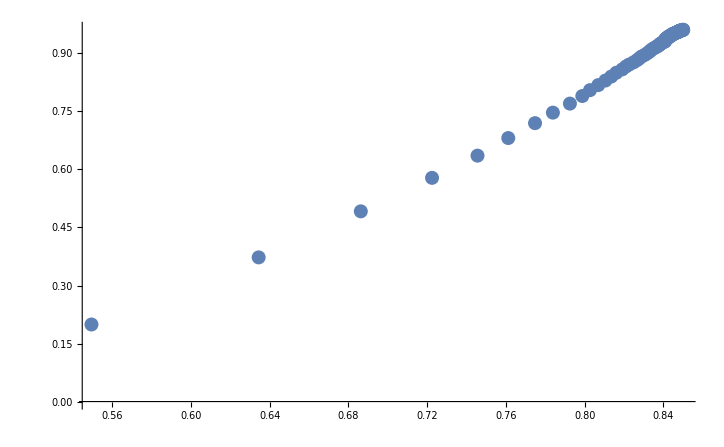

```mathematica
ListPlot[recallPrecisionFromStats/@mystats, PlotRange->All]
```